```mathematica
u090494e　荒井直幸　2014年11月18日
```

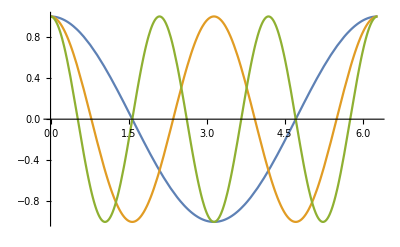

```mathematica
Plot[{Cos[x],Cos[2 x],Cos[3 x]},{x,0,2 Pi}]
```

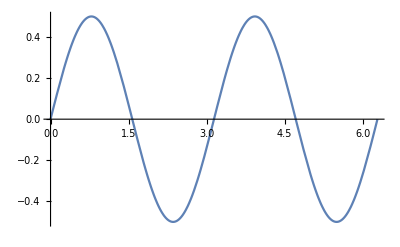

0

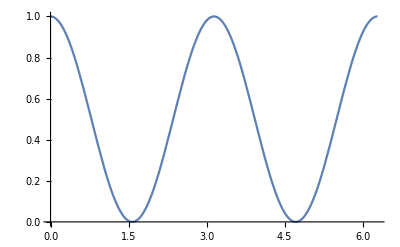

π

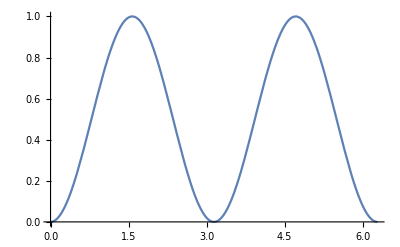

π

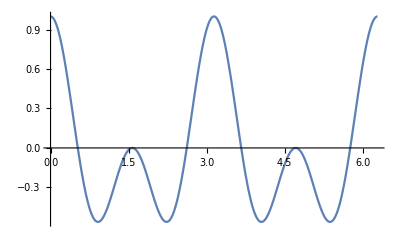

0

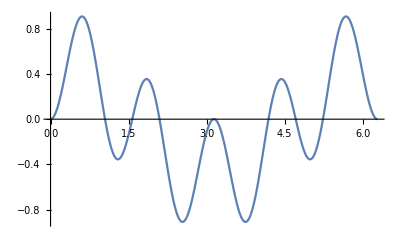

0

```mathematica
Plot[{Cos[x] Sin[x]},{x,0,2 Pi}]
Integrate[Cos[x] Sin[x],{x,0,2 Pi}]
Plot[{Cos[x] Cos[x]},{x,0,2 Pi}]
Integrate[Cos[x] Cos[x],{x,0,2 Pi}]
Plot[{Sin[x] Sin[x]},{x,0,2 Pi}]
Integrate[Sin[x] Sin[x],{x,0,2 Pi}]
Plot[{Cos[x] Cos[3 x]},{x,0,2 Pi}]
Integrate[Cos[x] Cos[3 x],{x,0,2 Pi}]
Plot[{Sin[2 x] Sin[3 x]},{x,0,2 Pi}]
Integrate[Sin[2 x] Sin[3 x],{x,0,2 Pi}]
```

```mathematica
課題１
```

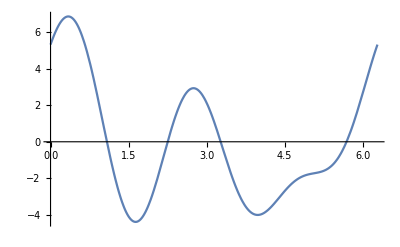

1.21

2.1

0.

3.21

2.31

0.

```mathematica
f1[x_]=2.1 Cos[x]+1.21 Sin[x]+3.21 Cos[2 x]+2.31 Sin[3 x];
Plot[f1[x],{x,0,2 Pi}]
Integrate[f1[x] Sin[x]/Pi,{x,0,2 Pi}]
Integrate[f1[x] Cos[x]/Pi,{x,0,2 Pi}]
Integrate[f1[x] Sin[2 x]/Pi,{x,0,2 Pi}]
Integrate[f1[x] Cos[2 x]/Pi,{x,0,2 Pi}]
Integrate[f1[x] Sin[3 x]/Pi,{x,0,2 Pi}]
Integrate[f1[x] Cos[3 x]/Pi,{x,0,2 Pi}]
```

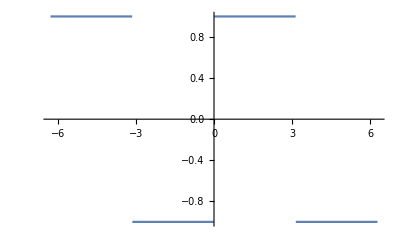

```mathematica
Plot[Sign[Sin[x]],{x,-2 Pi,2 Pi}]
```

{{-2 π,1},{-π,1},{-π,-1},{0,-1},{0,1},{π,1},{π,-1},{2 π,-1}}

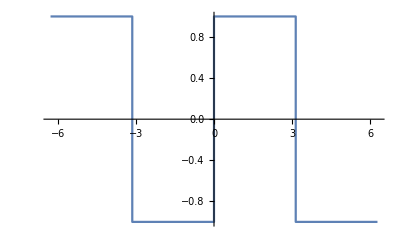

```mathematica
data1={{-2 Pi,1},{-Pi,1},{-Pi,-1},{0,-1},{0,1},{Pi,1},{Pi,-1},{2 Pi,-1}}
houkeiha=ListLinePlot[data1]
```

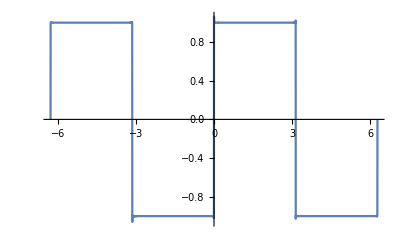

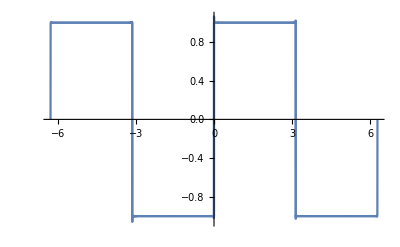

```mathematica
fourier1[n_]:=4/Pi∑_(i=0)^n Sin[(2 i+1) x]/(2 i+1)
Four1=Plot[fourier1[5000],{x,-2 Pi,2 Pi}]
Show[Four1,houkeiha]
```

(4 Sin[x])/π+(4 Sin[3 x])/(3 π)+(4 Sin[5 x])/(5 π)+(4 Sin[7 x])/(7 π)+(4 Sin[9 x])/(9 π)

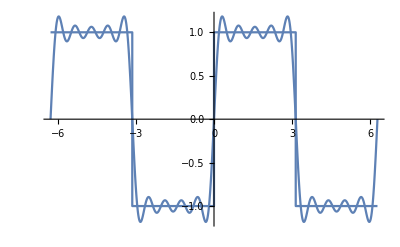

```mathematica
FTS=FourierTrigSeries[Sign[Sin[x]],x,10]
Four2=Plot[FTS,{x,-2 Pi,2 Pi}];
Show[Four2,houkeiha]
```

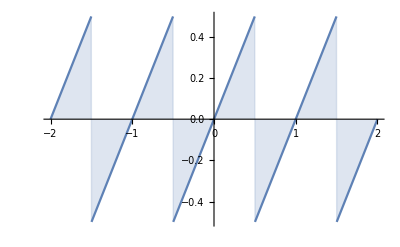

```mathematica
Plot[x-Round[x],{x,-2,2},Filling->Axis]
```

```mathematica
課題２
```

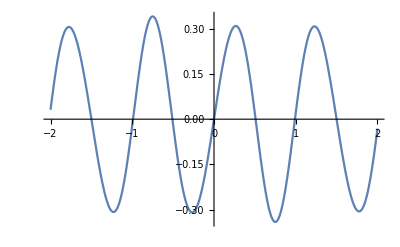

```mathematica
FTS1=FourierTrigSeries[x-Round[x],x,10];
Four3=Plot[FTS1,{x,-2,2}];
Show[Four3]
```

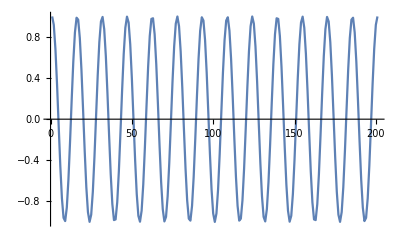

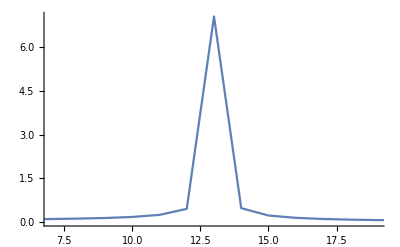

```mathematica
func1[x_]:=Cos[2 Pi n x/200];
n=13;
data1=Table[func1[x],{x,0,200}];
ListLinePlot[data1]
data2=Abs[Fourier[data1]];
data3=Rest[data2];
graph1=ListLinePlot[data3,PlotRange->{{7,19},All}]
```

```mathematica
課題３
```

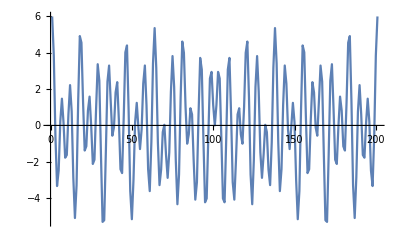

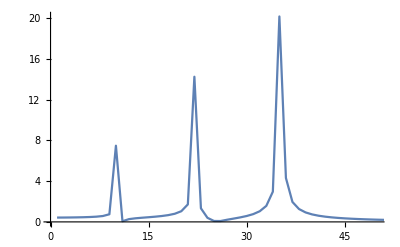

```mathematica
func2[x_]:=Cos[2 Pi o x/200];
o=10;
func3[x_]:=Cos[2 Pi p x/200];
p=22;
func4[x_]:=Cos[2 Pi q x/200];
q=35;
data4=Table[func2[x]+2 func3[x]+3 func4[x],{x,0,200}];
ListLinePlot[data4]
data5=Abs[Fourier[data4]];
data6=Rest[data5];
graph2=ListLinePlot[data6,PlotRange->{{0,50},All}]
```

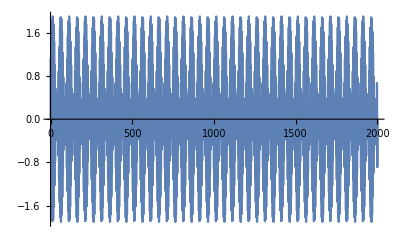

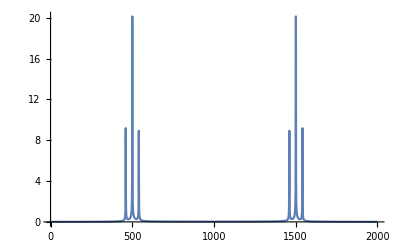

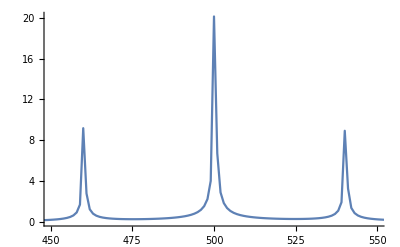

```mathematica
func3[x_]:=(1.0+0.9 Sin[2 Pi 40 x/2000]) Sin[2 Pi 500 x/2000];
data7=Table[func3[x],{x,0,2000}];
ListLinePlot[data7]
data8=Abs[Fourier[data7]];
data9=Rest[data8];
graph3=ListLinePlot[data9,PlotRange->{{0,2000},All}]
graph4=ListLinePlot[data9,PlotRange->{{450,550},All}]
```

```mathematica
課題４
```

```mathematica
AM波は
```

```mathematica
func4[x_]:=(1.0+0.9 Sin[2 Pi 40 x/2000]) Sin[2 Pi 500 x/2000];
data10=Table[func4[x],{x,0,2000}];
ListLinePlot[data10]
data11=Abs[Fourier[data10]];
data12=Rest[data11];
graph5=ListLinePlot[data12,PlotRange->{{0,2000},All}]
graph6=ListLinePlot[data12,PlotRange->{{450,550},All}]
```

-Graphics-

-Graphics-

-Graphics-

```mathematica
FM波は
```

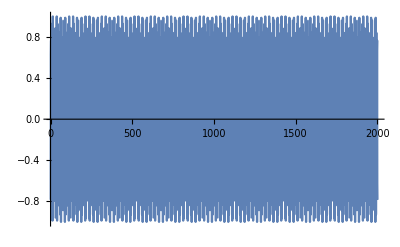

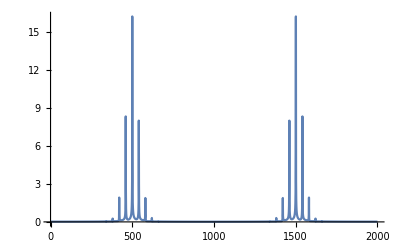

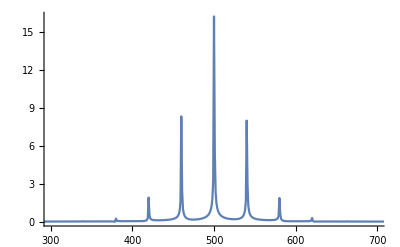

```mathematica
func5[x_]:=Sin[2 Pi 500 x/2000-0.9 Cos[2 Pi 40 x/2000]];
data13=Table[func5[x],{x,0,2000}];
ListLinePlot[data13]
data14=Abs[Fourier[data13]];
data15=Rest[data14];
graph7=ListLinePlot[data15,PlotRange->{{0,2000},All}]
graph8=ListLinePlot[data15,PlotRange->{{300,700},All}]
```

```mathematica
AM波のほうが占有する周波数幅が狭い
```